```mathematica
p=IdentityMatrix[9]-IdentityMatrix[9]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
p[[1,7]]=.5;
p[[1,5]]=.5;

p[[4,5]]=.5;
p[[4,1]]=.5;

p[[5,1]]=.5;
p[[5,7]]=.5;

p[[7,4]]=.5;
p[[7,9]]=.5;

p[[9,9]]=1;
```

```mathematica
p//MatrixForm
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Drop[p,{8},{8}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
p=Drop[%,{2,3},{2,3}]
```

{{0,0,0.5,0,0.5,0},{0.5,0,0.5,0,0,0},{0.5,0,0,0,0.5,0},{0,0,0,0,0,0},{0,0.5,0,0,0,0.5},{0,0,0,0,0,1}}

```mathematica
p//MatrixForm
```

(0 | 0 | 0.5 | 0 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
p={{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}
```

{{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}

```mathematica
π//N
```

3.14159

```mathematica
p//MatrixForm
```

```mathematica
(   {{1, 4, 5, 7, 9}}   )
({{1}, {4}, {5}, {7}, {9}})({{0, 0, 0.5, 0.5, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 1}})
```

```mathematica
d=DiscreteMarkovProcess[1,p]
```

DiscreteMarkovProcess[1,{{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}]

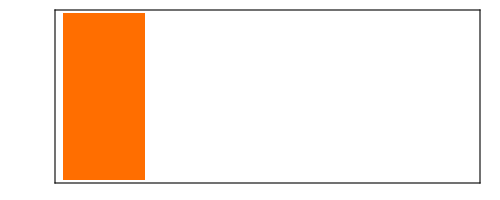
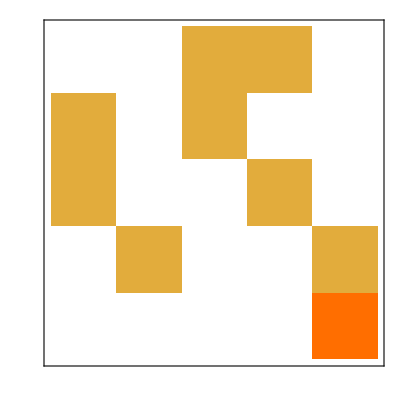
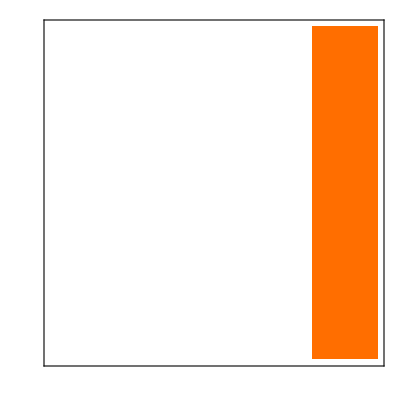
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0,∞}
HoldingTimeVariance | {0,0,0,0,∞}
Structural Properties | 
CommunicatingClasses | {5}, {1,…,4}
RecurrentClasses | {5}
TransientClasses | {1,…,4}
AbsorbingClasses | {5}
PeriodicClasses | None
Periods | {}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {2.33333,1.,1.66667,2.}
TransientVisitVariance | {22.8889,28.6667,26.2222,24.6667}
TransientTotalVisitMean | 3.21429
Limiting Properties | 
ReachabilityProbability | {0.571429,0.5,0.714286,1.,1.}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[d]
```

```mathematica
firstpassdist=FirstPassageTimeDistribution[DiscreteMarkovProcess[1,({{0, 0, 0.5, 0.5, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 1}})],5];
```

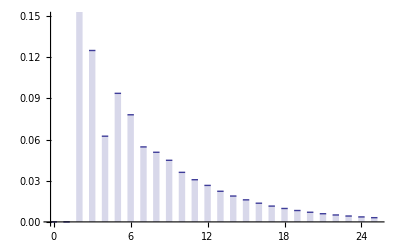

```mathematica
DiscretePlot[PDF[firstpassdist,k],{k,0,25},ExtentSize->.5]
```

```mathematica
Mean[firstpassdist]
```

7.

```mathematica
p//MatrixForm
```

```mathematica
"number 1"
```

number 1

```mathematica
P//MatrixForm
```

(0 | 0 | 0.5 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0
0.5 | 0 | 0 | 0.5 | 0
0 | 0.5 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 1)

```mathematica
Solve[{({{p1-0.5 p5-0.5 p7}, {-0.5 p1+p4-0.5 p5}, {-0.5 p1+p5-0.5 p7}, {-0.5 p4+p7-0.5 0}, {0}})==Transpose[{{1,1,1,1,0}}]},{p1,p4,p5,p7}]
```

{{p1→7.,p4→8.,p5→7.,p7→5.}}

```mathematica
Solve[{(IdentityMatrix[5]-({{0, 0, 0.5, 0.5, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 0}})).Transpose[{{p1,p4,p5,p7,p9}}]==Transpose[{{1,1,1,1,0}}]},{p1,p4,p5,p7,p9}]
```

{{p1→7.,p4→8.,p5→7.,p7→5.,p9→0.}}

```mathematica
Mean[{7,8,7,5}]//N
```

6.75

```mathematica
"number 2"
```

number 2

```mathematica
pabsord//MatrixForm
```

(0 | 0 | 0.5 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0
0.5 | 0 | 0 | 0.5 | 0
0 | 0.5 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 1)

```mathematica
Solve[{(({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}})-({{0, 0, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 0}})).Transpose[{{Subscript[ρ, 1],Subscript[ρ, 4],Subscript[ρ, 5],Subscript[ρ, 7],Subscript[ρ, 9]}}]==Transpose[{{0,0,0,0,1}}]},{Subscript[ρ, 1],Subscript[ρ, 4],Subscript[ρ, 5],Subscript[ρ, 7],Subscript[ρ, 9]}]//ReleaseHold
```

{{ρ_1→0.,ρ_4→0.142857,ρ_5→0.285714,ρ_7→0.571429,ρ_9→1.}}

```mathematica
{{p1->0.,p4->0.14285714285714285,p5->0.2857142857142857,p7->0.5714285714285714,p9->1.}}
```

```mathematica
{{p1->0.,p4->0.14285714285714285,p5->0.2857142857142857,p7->0.5714285714285714,p9->1.}}//Normal
```

```mathematica
{{p1->0.,p4->0.14285714285714285,p5->0.2857142857142857,p7->0.5714285714285714,p9->1.}}/.
```

```mathematica
"number 3"
```

```mathematica
pp={{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{.5,0,0,.5,0}};
```

```mathematica
pp//MatrixForm
```

(0 | 0 | 0.5 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0
0.5 | 0 | 0 | 0.5 | 0
0 | 0.5 | 0 | 0 | 0.5
0.5 | 0 | 0 | 0.5 | 0)

```mathematica
dd=DiscreteMarkovProcess[1,pp]
```

DiscreteMarkovProcess[1,{{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0.5,0,0,0.5,0}}]

```mathematica
Graph[dd,VertexLabels->{1->Placed["1",Center],2->Placed["4",Center],3->Placed["5",Center],4->Placed["7",Center],5->Placed["9",Center]},EdgeLabels->{1->4->Placed[".5",{.5,{-.5,0}}],4->5->Placed[".5",{.5,{-.1,0}}],4->2->Placed[".5",{.5,{-.5,0}}],3->4->Placed[".5",{.5,{-.5,0}}],4->5->Placed[".5",{.5,{-.5,0}}],3->4->Placed[".5",{.5,{-.5,0}}],3->1->Placed[".5",{.5,{-.5,0}}],2->1->Placed[".5",{.5,{-.5,0}}],5->1->Placed[".5",{.5,{-.5,0}}],5->4->Placed[".5",{.5,{-.5,0}}]}]
```

-Graphics-

```mathematica
Graph[dd,VertexLabels->{1->Placed["1",Center],2->Placed["4",Center],3->Placed["5",Center],4->Placed["7",Center],5->Placed["9",Center]}]
```

-Graphics-

```mathematica
"irreducible, finite, stationary distribution, aperiodic because 3->1->3 and 3->4->2->3 hence limiting = stationary"
```

-Graphics-

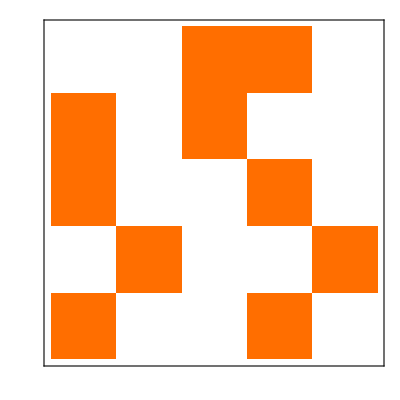
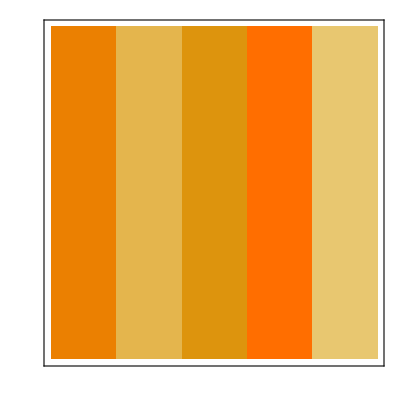
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0,0}
HoldingTimeVariance | {0,0,0,0,0}
Structural Properties | 
CommunicatingClasses | {1,…,5}
RecurrentClasses | {1,…,5}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[dd]
```

```mathematica
MatrixPower[pp,100]//MatrixForm
```

```mathematica
({{0.23809523809523808, 0.14285714285714285, 0.1904761904761905, 0.2857142857142857, 0.14285714285714285}, {0.23809523809523808, 0.14285714285714285, 0.19047619047619047, 0.2857142857142857, 0.14285714285714285}, {0.23809523809523808, 0.14285714285714285, 0.1904761904761905, 0.2857142857142857, 0.14285714285714285}, {0.23809523809523808, 0.14285714285714285, 0.19047619047619047, 0.2857142857142857, 0.14285714285714285}, {0.23809523809523808, 0.14285714285714285, 0.1904761904761905, 0.2857142857142857, 0.14285714285714285}})~Round~.001
```

```mathematica
{{0.23800000000000002,0.14300000000000002,0.19,0.28600000000000003,0.14300000000000002},{0.23800000000000002,0.14300000000000002,0.19,0.28600000000000003,0.14300000000000002},{0.23800000000000002,0.14300000000000002,0.19,0.28600000000000003,0.14300000000000002},{0.23800000000000002,0.14300000000000002,0.19,0.28600000000000003,0.14300000000000002},{0.23800000000000002,0.14300000000000002,0.19,0.28600000000000003,0.14300000000000002}}//Rationalize//N
```

```mathematica
{{0.238,0.143,0.19,0.286,0.143},{0.238,0.143,0.19,0.286,0.143},{0.238,0.143,0.19,0.286,0.143},{0.238,0.143,0.19,0.286,0.143},{0.238,0.143,0.19,0.286,0.143}}//MatrixForm
```

```mathematica
({{0.238, 0.143, 0.19, 0.286, 0.143}, {0.238, 0.143, 0.19, 0.286, 0.143}, {0.238, 0.143, 0.19, 0.286, 0.143}, {0.238, 0.143, 0.19, 0.286, 0.143}, {0.238, 0.143, 0.19, 0.286, 0.143}})//Rationalize
```

{{119/500,143/1000,19/100,143/500,143/1000},{119/500,143/1000,19/100,143/500,143/1000},{119/500,143/1000,19/100,143/500,143/1000},{119/500,143/1000,19/100,143/500,143/1000},{119/500,143/1000,19/100,143/500,143/1000}}

```mathematica
"probability of returning to 1 if you've hit 1"
```

```mathematica
Solve[{(({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}})-({{0, 0, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0.5, 0, 0, 0.5, 0}})).Transpose[{{p1,p4,p5,p7,p9}}]==Transpose[{{1,1,1,1,1}}]},{p1,p4,p5,p7,p9}]//ReleaseHold
```

{{p1→1.,p4→3.4,p5→3.8,p7→4.6,p9→3.8}}

```mathematica
{{p1},{-0.5 p1+p4-0.5 p5},{-0.5 p1+p5-0.5 p7},{-0.5 p4+p7-0.5 p9},{p9}}==
```

```mathematica
Thread[{p1,-0.5 p1+p4-0.5 p5,-0.5 p1+p5-0.5 p7,-0.5 p4+p7-0.5 p9,p9}=={0,0,0,0,1}]
```

```mathematica
{p1==0,-0.5 p1+p4-0.5 p5==0,-0.5 p1+p5-0.5 p7==0,-0.5 p4+p7-0.5 p9==0,p9==1}/.{p1->Subscript[π, 1],p4->Subscript[π, 4],p5->Subscript[π, 5],p7->Subscript[π, 7],p9->Subscript[π, 9]}
```

```mathematica
{Subscript[π, 1]==0,-0.5 Subscript[π, 1]+Subscript[π, 4]-0.5 Subscript[π, 5]==0,-0.5 Subscript[π, 1]+Subscript[π, 5]-0.5 Subscript[π, 7]==0,-0.5 Subscript[π, 4]+Subscript[π, 7]-0.5 Subscript[π, 9]==0,Subscript[π, 9]==1}//MatrixForm
```

(π_1==0
-0.5 π_1+π_4-0.5 π_5==0
-0.5 π_1+π_5-0.5 π_7==0
-0.5 π_4+π_7-0.5 π_9==0
π_9==1)

```mathematica
{{p1}=={0},{-0.5 p1+p4-0.5 p5}=={0},{-0.5 p1+p5-0.5 p7}=={0},{-0.5 p4+p7-0.5 p9}=={0},{p9}=={1}}[[1]]
```

```mathematica
{p1}=={0}//Flatten
```

```mathematica
{p1}=={0}
```

```mathematica
{p1}=={0}//FullForm
```

```mathematica
(({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}})-({{0, 0, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 0}})).Transpose[{{p1,p4,p5,p7,p9}}]
```

```mathematica
{{p1},{-0.5 p1+p4-0.5 p5},{-0.5 p1+p5-0.5 p7},{-0.5 p4+p7-0.5 p9},{p9}}//Flatten
```

{p1,-0.5 p1+p4-0.5 p5,-0.5 p1+p5-0.5 p7,-0.5 p4+p7-0.5 p9,p9}

```mathematica
ρ
```

```mathematica
(Subscript[π, 1],Subscript[π, 4],Subscript[π, 5],Subscript[π, 7],Subscript[π, 9])/.{π->ρ}
```

Syntax::sntxf: "(" cannot be followed by "π_1, π_4, π_5, π_7, TraditionalForm`π_9)""".

Syntax::tsntxi: "π_1, π_4, π_5, π_7, TraditionalForm`π_9" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
Subscript[π, 1],Subscript[π, 4],Subscript[π, 5],Subscript[π, 7],Subscript[π, 9]/.{π->ρ}
```

Syntax::tsntxi: "π_1, π_4, π_5, π_7, TraditionalForm`π_9/.{π -> ρ}" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
{{Subscript[π, 1]->7,Subscript[π, 4]->8,Subscript[π, 5]->7,Subscript[π, 7]->5,Subscript[π, 9]->0}}/.π->ρ
```

```mathematica
{Subscript[ρ, 1]->7,Subscript[ρ, 4]->8,Subscript[ρ, 5]->7,Subscript[ρ, 7]->5,Subscript[ρ, 9]->0}//MatrixForm
```

```mathematica
({{Subscript[ρ, 1]}, {Subscript[ρ, 4]}, {Subscript[ρ, 5]}, {Subscript[ρ, 7]}, {Subscript[ρ, 9]}})
```